# Distribution

```mathematica
features=Import["K:\\Learning\\Spring_2014\\EECE5698_MachLearning\\proj\\yelp-ml\\data\\feature_review_training-20000.csv"][[2;;,All]]
```

{{9,5,12,2,0.607,4.,75,4.35,185,2},{24,5,43,11,0.785875,4.,319,4.86,9,0},{48,4,56,11,-0.141763,4.5,6,3.89,156,8},{59,5,13,8,0.386166,3.5,29,3.89,25,0},{70,3,159,20,0.284021,3.5,121,3.87,68,3},{72,3,75,8,0.367805,2.,7,3.45,347,20},{84,4,59,7,0.382104,4.,185,3.83,6,0},{89,5,56,6,0.208897,3.5,82,3.86,417,35},{115,5,66,13,0.7245,4.5,17,3.9,2041,49},«19983»,{334833,5,68,6,0.55719,3.5,57,5.,8,0},{334858,5,31,4,0.112626,4.5,18,5.,5,0},{334861,5,14,10,0.746605,4.5,7,4.98,63,0},{334949,5,15,4,0.484492,3.,195,5.,1,0},{334950,5,287,31,0.255525,4.,455,3.63,156,4},{334990,4,120,27,0.310194,4.5,150,3.66,41,1},{334998,4,23,3,0.572415,4.5,112,3.74,228,9},{335009,3,29,4,0.815445,3.5,148,3.64,292,2}}

## Word Count

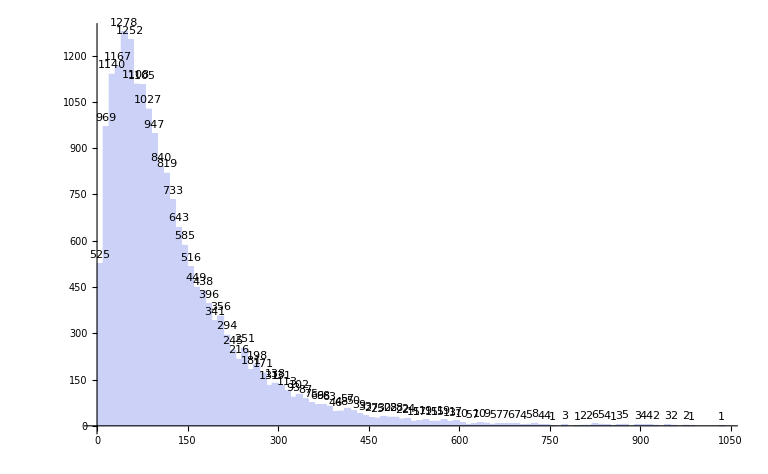

126.981

```mathematica
Histogram[features[[All,3]],LabelingFunction->Above]
N[Mean[features[[All,3]]]]
```

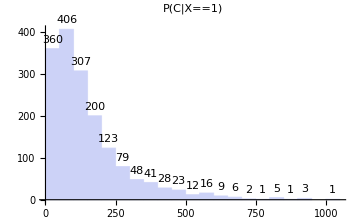
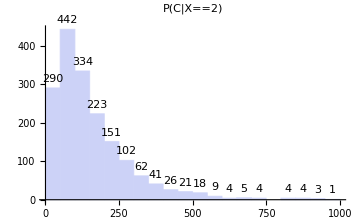
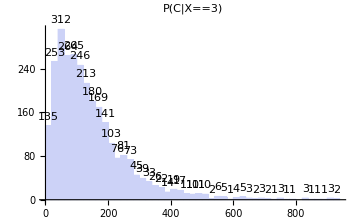
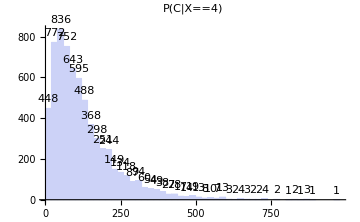
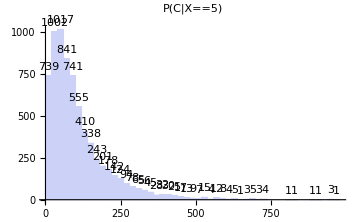

```mathematica
ratings=Range[1,5,1];
Table[
Histogram[Select[features,#[[2]]==r&][[All,3]],LabelingFunction->Above,PlotLabel->P[C|X==r],ImageSize->Medium],
{r,ratings}
]
```

## UCase Count

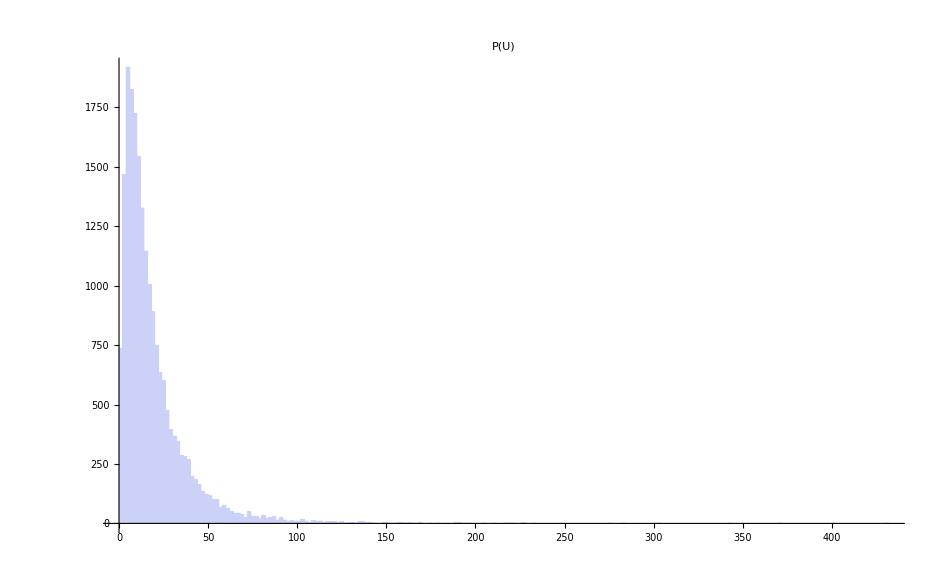

18.5203

```mathematica
Histogram[features[[All,4]],PlotLabel->P[U],ImageSize->Large]
N[Mean[features[[All,4]]]]
```

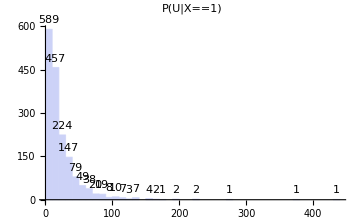
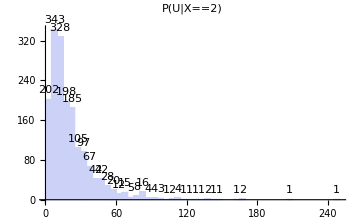
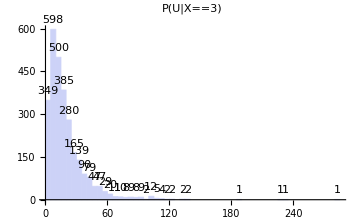
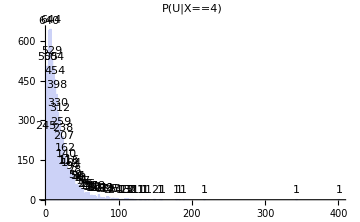
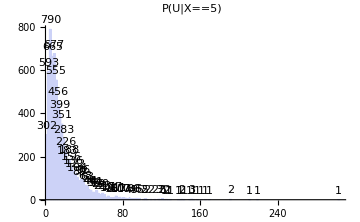

```mathematica
ratings=Range[1,5,1];
Table[
Histogram[Select[features,#[[2]]==r&][[All,4]],LabelingFunction->Above,PlotLabel->P[U|X==r],ImageSize->Medium],
{r,ratings}
]
```

## Prior of Classes

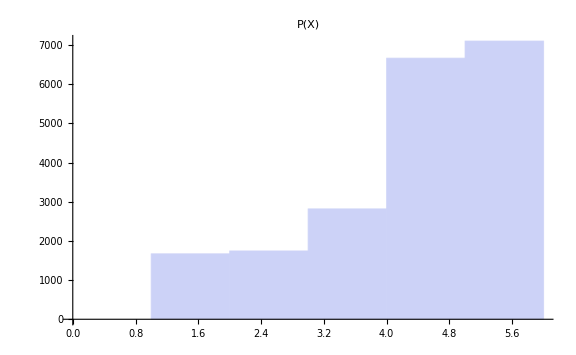

3.78915

```mathematica
Histogram[features[[All,2]],PlotLabel->P[X],ImageSize->Large]
N[Mean[features[[All,2]]]]
```

## Polarity

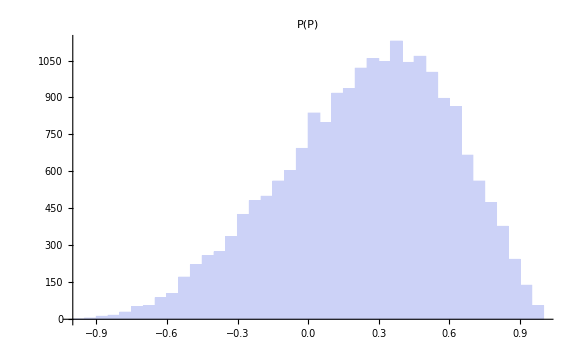

0.244982

```mathematica
Histogram[features[[All,5]],PlotLabel->P[P],ImageSize->Large]
N[Mean[features[[All,5]]]]
```

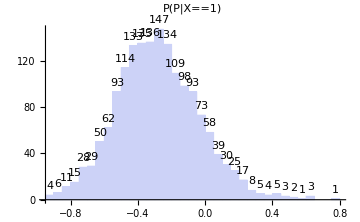
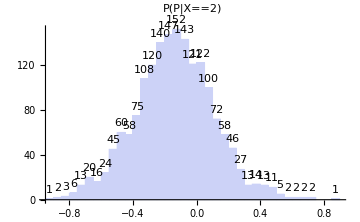
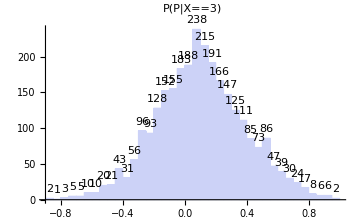
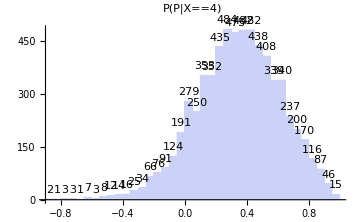
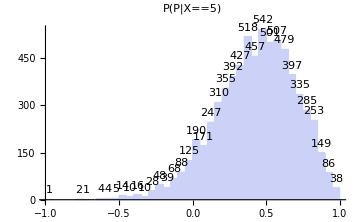
{-Graphics-
-0.282755,-Graphics-
-0.139778,-Graphics-
0.100395,-Graphics-
0.343896,-Graphics-
0.428178}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,5]],LabelingFunction->Above,PlotLabel->P[P|X==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,5]]]]}],
{r,ratings}
]
```

## Biz Stars

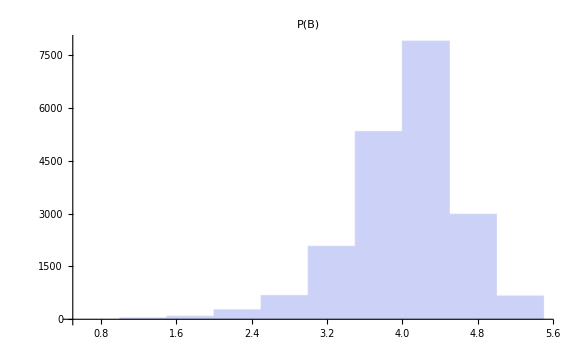

3.77665

```mathematica
Histogram[features[[All,6]],PlotLabel->P[B],ImageSize->Large]
N[Mean[features[[All,6]]]]
```

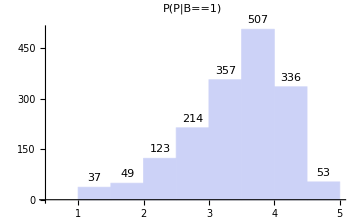
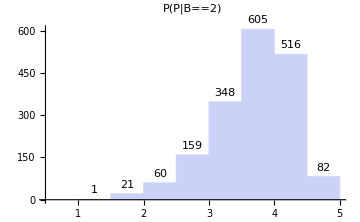
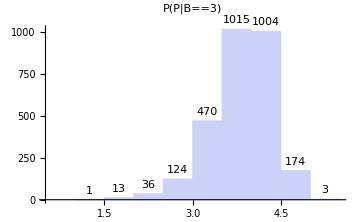
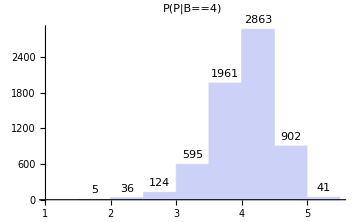
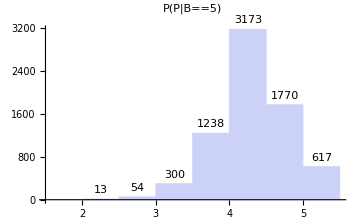
{-Graphics-
3.17393,-Graphics-
3.42885,-Graphics-
3.58415,-Graphics-
3.79255,-Graphics-
4.06643}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,6]],LabelingFunction->Above,PlotLabel->P[P|B==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,6]]]]}],
{r,ratings}
]
```

## Biz Reviews Count

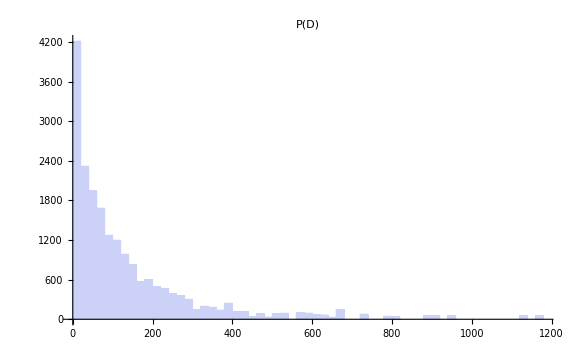

139.502

```mathematica
Histogram[features[[All,7]],PlotLabel->P[D],ImageSize->Large]
N[Mean[features[[All,7]]]]
```

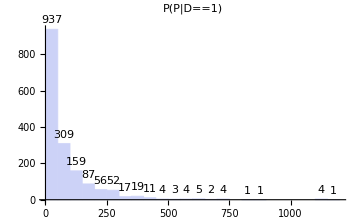
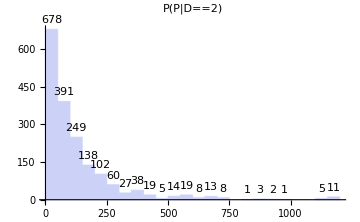
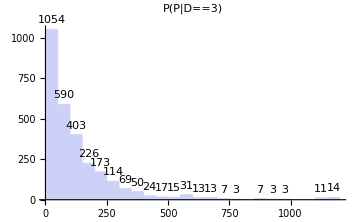
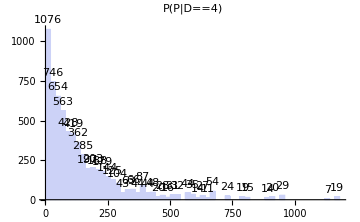
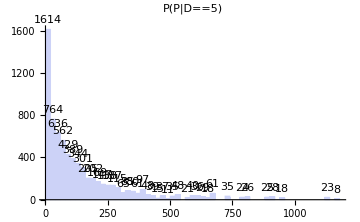
{-Graphics-
81.5621,-Graphics-
129.512,-Graphics-
131.598,-Graphics-
150.931,-Graphics-
148.275}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,7]],LabelingFunction->Above,PlotLabel->P[P|D==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,7]]]]}],
{r,ratings}
]
```

## Usr Average Stars

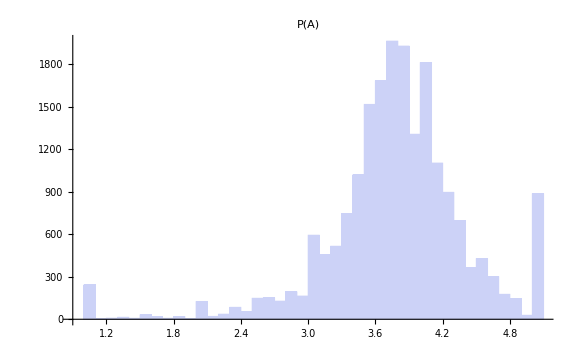

3.76322

```mathematica
Histogram[features[[All,8]],PlotLabel->P[A],ImageSize->Large]
N[Mean[features[[All,8]]]]
```

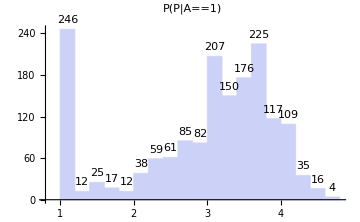
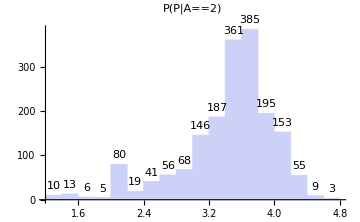
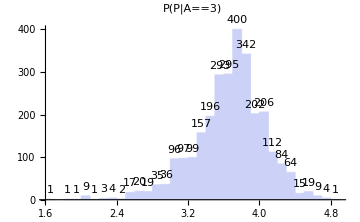
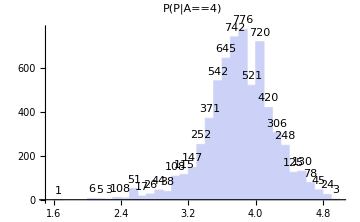
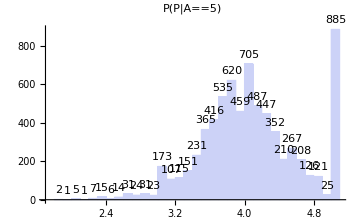
{-Graphics-
2.91758,-Graphics-
3.41748,-Graphics-
3.65562,-Graphics-
3.7978,-Graphics-
4.05864}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,8]],LabelingFunction->Above,PlotLabel->P[P|A==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,8]]]]}],
{r,ratings}
]
```

## Usr Review Count

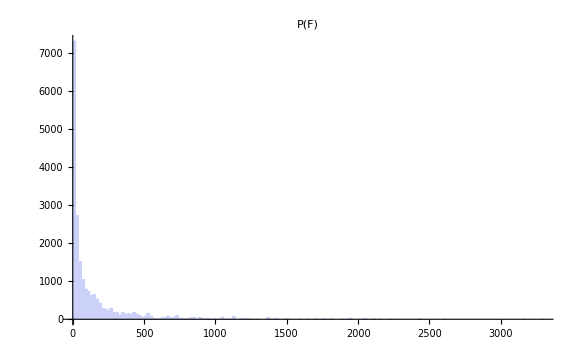

130.424

```mathematica
Histogram[features[[All,9]],PlotLabel->P[F],ImageSize->Large]
N[Mean[features[[All,9]]]]
```

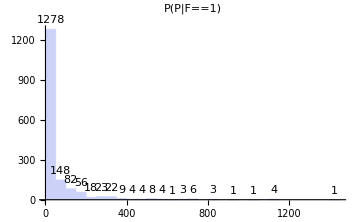
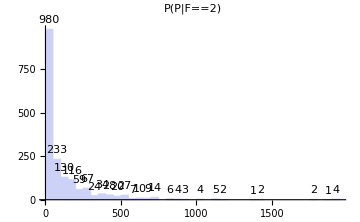
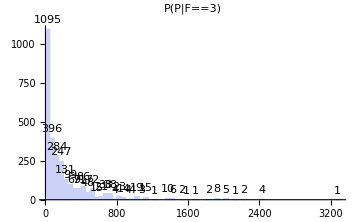
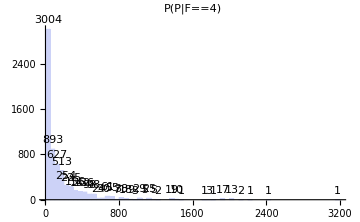
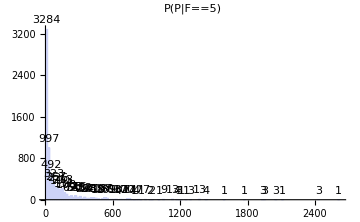
{-Graphics-
56.0871,-Graphics-
125.253,-Graphics-
199.614,-Graphics-
158.598,-Graphics-
96.0161}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,9]],LabelingFunction->Above,PlotLabel->P[P|F==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,9]]]]}],
{r,ratings}
]
```

## Usr Fans

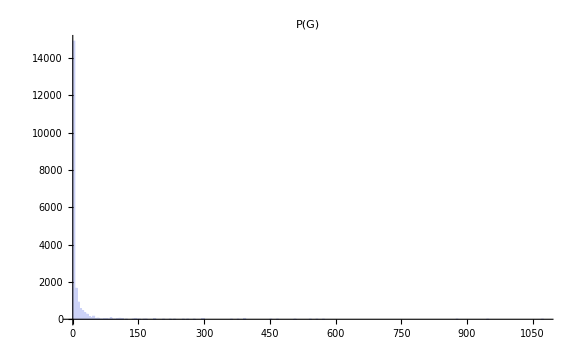

8.10735

```mathematica
Histogram[features[[All,10]],PlotLabel->P[G],ImageSize->Large]
N[Mean[features[[All,10]]]]
```

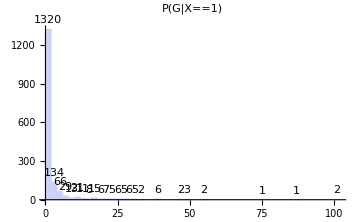
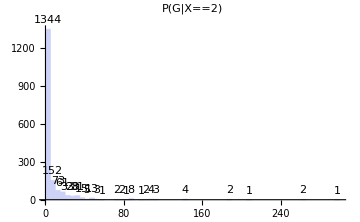
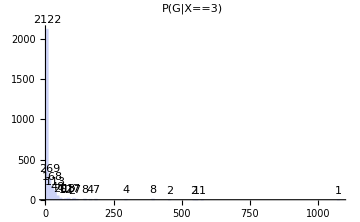
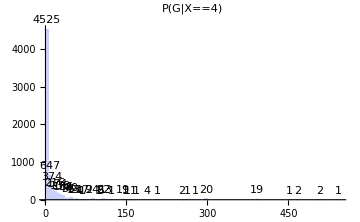
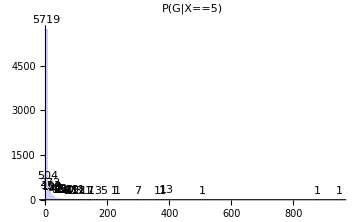
{-Graphics-
2.27685,-Graphics-
6.74442,-Graphics-
12.5743,-Graphics-
10.0257,-Graphics-
6.29393}

```mathematica
ratings=Range[1,5,1];
Table[
Column[{Histogram[Select[features,#[[2]]==r&][[All,10]],LabelingFunction->Above,PlotLabel->P[G|X==r],ImageSize->Medium],N[Mean[Select[features,#[[2]]==r&][[All,10]]]]}],
{r,ratings}
]
```